```mathematica
γ[t_]:=1/Sqrt[1-((xp'[t])^2+(yp'[t])^2+(zp'[t])^2)]
```

```mathematica
Z[t_]:={{t},{xp[t]},{yp[t]},{zp[t]}}
```

```mathematica
X[t_]:={{t},{x},{y},{z}}
```

```mathematica
V[t_]:=D[Z[t],t]
```

```mathematica
U[t_]:=γ[t]D[Z[t],t]
```

```mathematica
B[v_]:=({{γ[t], -γ[t]*v[[1,1]], -γ[t]*v[[2,1]], -γ[t]*v[[3,1]]}, {-γ[t]*v[[1,1]], 1+(γ[t]-1)v[[1,1]]^2/Sqrt[v[[1,1]]^2+v[[2,1]]^2+v[[3,1]]^2], (γ[t]-1)(v[[1,1]]*v[[2,1]])/Sqrt[v[[1,1]]^2+v[[2,1]]^2+v[[3,1]]^2], (γ[t]-1)(v[[1,1]]*v[[3,1]])/Sqrt[v[[1,1]]^2+v[[2,1]]^2+v[[3,1]]^2]}, {-γ[t]*v[[2,1]], (γ[t]-1)(v[[1,1]]*v[[2,1]])/Sqrt[v[[1,1]]^2+v[[2,1]]^2+v[[3,1]]^2], 1+(γ[t]-1)v[[3,1]]^2/Sqrt[v[[1,1]]^2+v[[2,1]]^2+v[[3,1]]^2], (γ[t]-1)(v[[2,1]]*v[[3,1]])/Sqrt[v[[1,1]]^2+v[[2,1]]^2+v[[3,1]]^2]}, {-γ[t]*v[[3,1]], (γ[t]-1)(v[[1,1]]*v[[3,1]])/Sqrt[v[[1,1]]^2+v[[2,1]]^2+v[[3,1]]^2], (γ[t]-1)(v[[2,1]]*v[[3,1]])/Sqrt[v[[1,1]]^2+v[[2,1]]^2+v[[3,1]]^2], 1+(γ[t]-1)v[[3,1]]^2/Sqrt[v[[1,1]]^2+v[[2,1]]^2+v[[3,1]]^2]}})
```

```mathematica
a=0;
```

```mathematica
Φ[x_]:=1/(Sqrt[x[[2,1]]^2+x[[3,1]]^2+x[[4,1]]^2]+a)
```

```mathematica
Fs[t_,x_,z_,v_]:=Φ[B[v].(x-z)]
```

```mathematica
Φs = Fs[t,X[t],Z[t],V[t]]//Simplify;
```

```mathematica
Ψx=D[Φs ,x];
Ψy=D[Φs ,y];
Ψz=D[Φs ,z];
Π = D[Φs ,t];
```

```mathematica
dvΨi = D[V[t][[2,1]],t]D[Ψx,V[t][[2,1]]]+D[V[t][[3,1]],t]D[Ψy,V[t][[3,1]]]+D[V[t][[4,1]],t]D[Ψz,V[t][[4,1]]];
dvΠ = D[V[t][[2,1]],t]D[Π,V[t][[2,1]]]+D[V[t][[3,1]],t]D[Π,V[t][[3,1]]]+D[V[t][[4,1]],t]D[Π,V[t][[4,1]]];
```

```mathematica
GetPower[f0_]:=Module[{f=f0},
fs = Simplify[f/.{
xp'[t]->0.1,yp'[t]->0.2,zp'[t]->0.1,
xp''[t]->-0.2,yp''[t]->0.1,zp''[t]->0.1,
xp[t]->0,yp[t]->0,zp[t]->0}]//FullSimplify;
    Block[{ x=r Sin[θ]Cos[φ],y = r Sin[θ]Sin[φ],z = r Cos[θ]},
Nom=Exponent[ExpandAll[Numerator[fs//Simplify]],r];
Denom=Exponent[ExpandAll[Denominator[fs//Simplify]],r];
Nom-Denom]]
```

```mathematica
GetPower[Π]
```

-1

```mathematica
GetPower[Ψx]
```

-2

```mathematica
GetPower[Φs]
```

-1

```mathematica
GetPower[dvΠ]
```

-1

```mathematica
GetPower[dvΨi]
```

-2

```mathematica
Limit[temp[x],x->0,Direction->"FromAbove"]//N
```

∞

```mathematica
Limit[temp[x],x->0,Direction->"FromBelow"]//N
```

-∞

```mathematica
temp[s_]:=Piecewise[{{-(15 √(5/(185-80 √3+48 √5-24 √15)) (-185+80 √3-48 √5+24 √15))/(2 (15 a+√(5 (185-80 √3+48 √5-24 √15)) s)^2), s>0}, {(15 √(5/(185-80 √3+48 √5-24 √15)) (-185+80 √3-48 √5+24 √15))/(2 (-15 a+√(5 (185-80 √3+48 √5-24 √15)) s)^2), s<0}}]
```

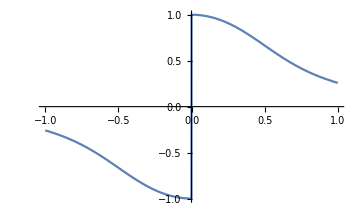

```mathematica
Plot[2/π ArcTan[temp[s]]/.a->0.01,{s,-1,1},PlotRange->All]
```